## 获取所有卷积核

```mathematica
paths=Import["E:\\GitHub\\Alpha_blokus_USTC\\_data\\chesses\\TOC.txt","List"];
```

```mathematica
cores={Import[#~~"\\O.csv","CSV"],Import[#~~"\\B.csv","CSV"],Import[#~~"\\C.csv","CSV"]}&/@paths;
```

## 棋盘的基本处理函数

```mathematica
len=14;
```

```mathematica
GetIndex[mat_,index_]:=mat/.{i_/;i==index->1,i_/;i≠index->0}
```

```mathematica
matTest=RandomChoice[{#1,#2,1-#1-#2}->{1,2,0},{14,14}]&[0.05,0.05];
```

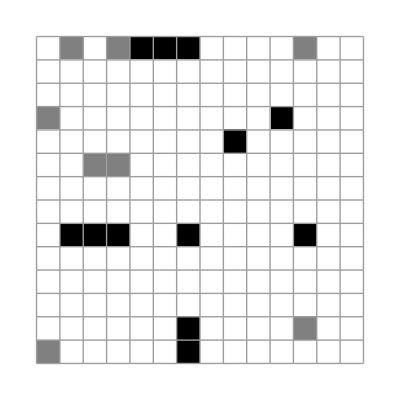
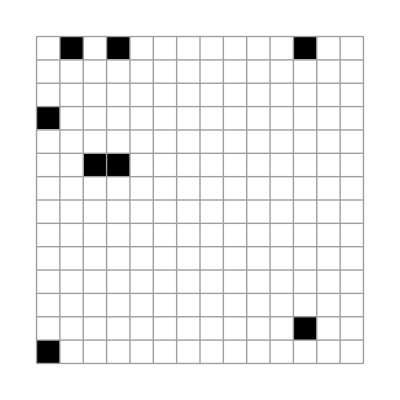
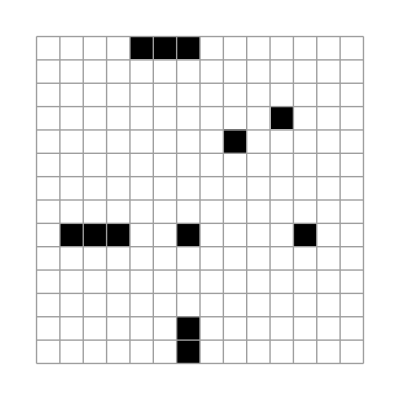

```mathematica
ArrayPlot[#,Mesh->All]&/@{matTest,GetIndex[matTest,1],GetIndex[matTest,2]}
```

## 获得可以落子的点

注：得到的是一个21 20 20的数组。

```mathematica
transform[m_]:=mᵀ
```

```mathematica
GetPointCanPutChess[mat_,color_,{coreO_,coreB_,coreC_}](*棋盘，自己的颜色*):=Module[
{matme=GetIndex[mat,color],matother=GetIndex[mat,3-color],pad=3,k={},cannotPut,bondLink,havecorner},
cannotPut=ListConvolve[Reverse/@Reverse@coreO,ArrayPad[mat,pad,1]]/.{n_/;n>0->True,n_/;n==0->False};
bondLink=ListConvolve[Reverse/@Reverse@coreB,ArrayPad[matme,pad,0]]/.{n_/;n>0->True,n_/;n==0->False};
havecorner=ListConvolve[Reverse/@Reverse@coreC,ArrayPad[matme,pad,0]]/.{n_/;n>0->True,n_/;n==0->False};
Table[Not[cannotPut⟦i,j⟧]∧Not[bondLink⟦i,j⟧]∧havecorner⟦i,j⟧,{i,1,len},{j,1,len}]/.{False->0,True->1}
]
```

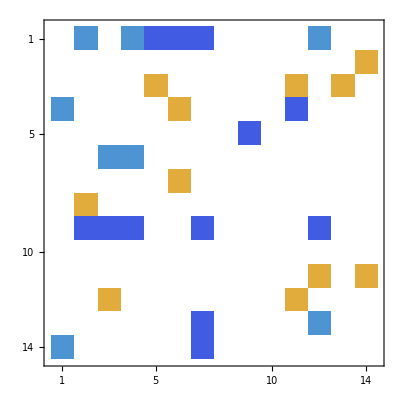

```mathematica
MatrixPlot[-matTest+GetPointCanPutChess[matTest,1,cores⟦#⟧],PlotLabel->MatrixPlot[cores⟦#,1⟧,Mesh->All,ImageSize->64]]&[10]
```

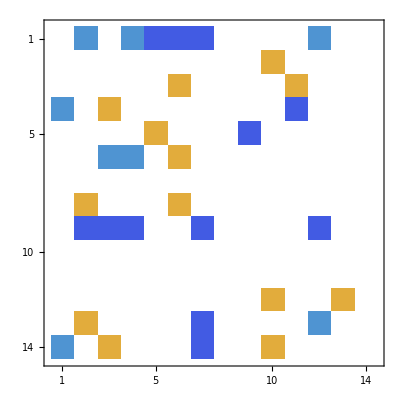
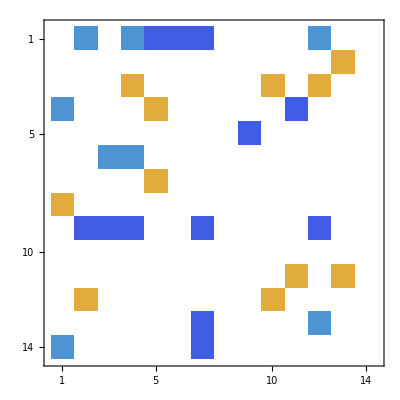
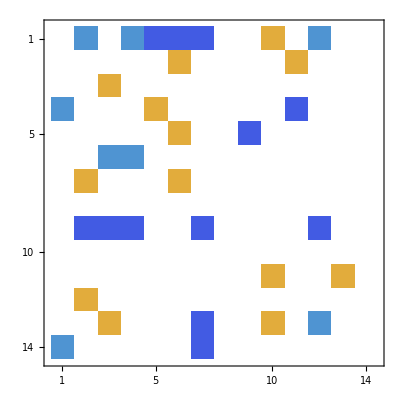
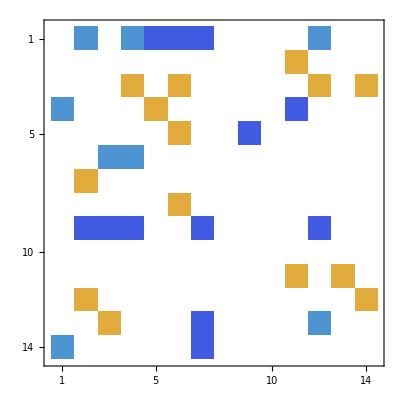
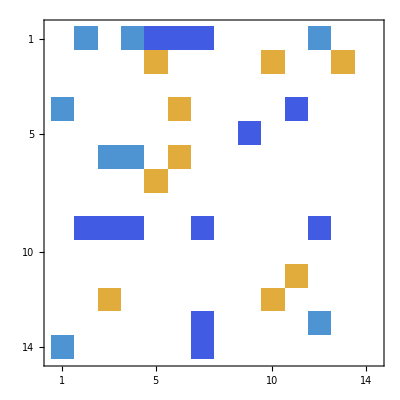
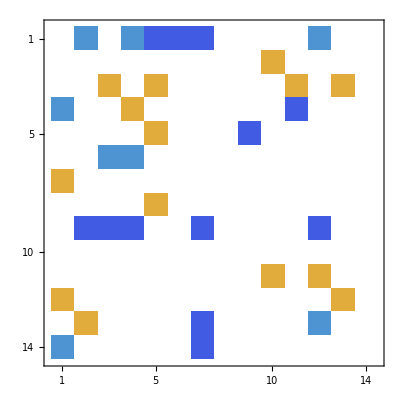
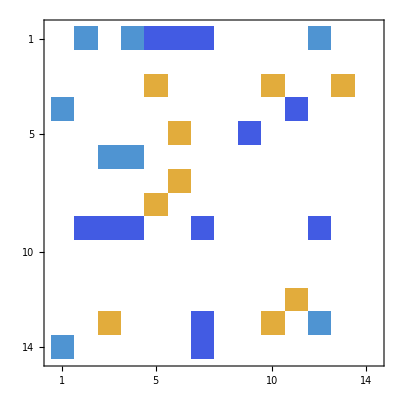
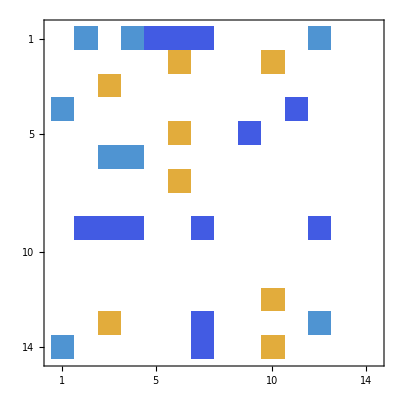
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[-matTest+GetPointCanPutChess[matTest,1,cores⟦i⟧],PlotLabel->MatrixPlot[Reverse@cores⟦i,1⟧ᵀ,Mesh->All,ImageSize->64]],{i,10,20}]
```

### 一套卷积核的结构

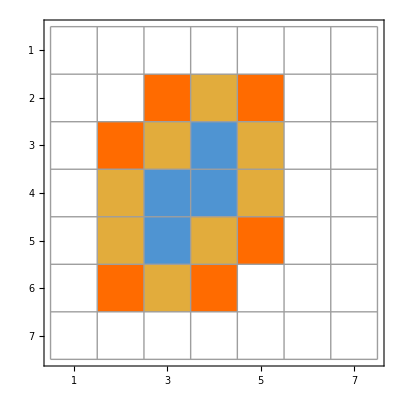

```mathematica
MatrixPlot[-cores⟦#,1⟧+cores⟦#,2⟧+2cores⟦#,3⟧,Mesh->All]&[10]
```

## 落子

```mathematica
PutChess[mat_,index_,p_,type_]:=Module[{pAdd=Table[0,{len},{len}]},
pAdd⟦p⟦1⟧,p⟦2⟧⟧=1;
pAdd=ListConvolve[cores⟦type,1⟧,ArrayPad[pAdd,3]]*index;
mat+pAdd
]
```

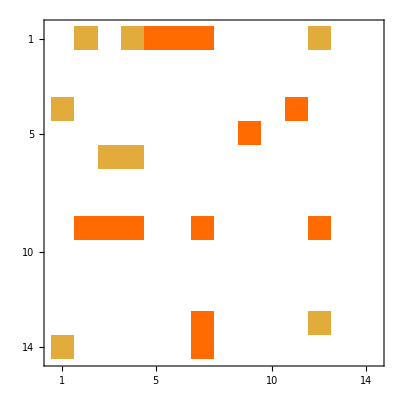
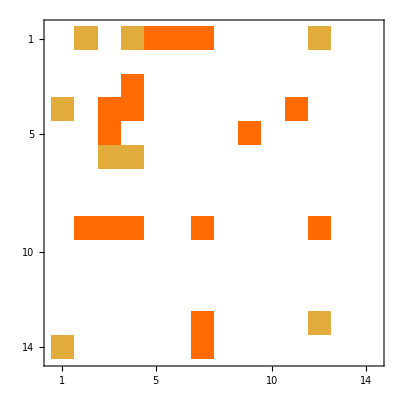
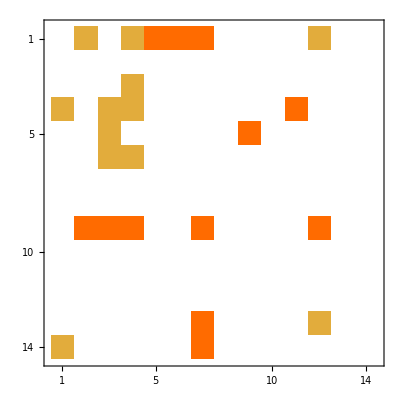

```mathematica
MatrixPlot/@{matTest,PutChess[matTest,2,{4,4},10],PutChess[matTest,1,{4,4},10]}
```

## 静态评分函数

```mathematica
Score[mat_,index_]:=Module[{m=GetIndex[mat,index],n,canputs},
n=Total@Total@m;
canputs=Total[GetPointCanPutChess[mat,index,#]&/@cores,∞];
n+0.5*canputs
]
```

```mathematica
Score[matTest,#]&/@{1,2}
```

{1398.5,1657.5}

### 对每个点评分

```mathematica
ScoreForPoint[mat_,points_,index_,type_]:=Table[
If[points⟦i,j⟧≠0,(Score[PutChess[mat,index,{i,j},type],index]-Score[PutChess[mat,index,{i,j},type],3-index])-(Score[mat,index]-Score[mat,3-index]),0]
,{i,1,len},{j,1,len}]
```

```mathematica
MatrixForm[data=ScoreForPoint[mats,GetPointCanPutChess[mats,1,cores⟦#⟧],1,#]&[3]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

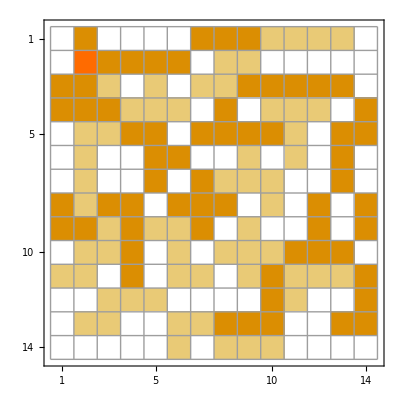

```mathematica
MatrixPlot[mats+data,Mesh->All]
```

```mathematica
mats=({{0, 2, 0, 0, 0, 0, 2, 2, 2, 1, 1, 1, 1, 0}, {0, 0, 2, 2, 2, 2, 0, 1, 1, 0, 0, 0, 0, 0}, {2, 2, 1, 0, 1, 0, 1, 1, 2, 2, 2, 2, 2, 0}, {2, 2, 2, 1, 1, 1, 0, 2, 0, 1, 1, 1, 0, 2}, {0, 1, 1, 2, 2, 0, 2, 2, 2, 2, 1, 0, 2, 2}, {0, 1, 0, 0, 2, 2, 0, 0, 1, 0, 1, 0, 2, 0}, {0, 1, 0, 0, 2, 0, 2, 1, 1, 1, 0, 0, 2, 0}, {2, 1, 2, 2, 0, 2, 2, 2, 0, 1, 0, 2, 0, 2}, {2, 2, 1, 2, 1, 1, 2, 0, 1, 0, 0, 2, 0, 2}, {0, 1, 1, 2, 0, 1, 0, 1, 1, 1, 2, 2, 2, 0}, {1, 1, 0, 2, 0, 1, 1, 0, 1, 2, 1, 1, 1, 2}, {0, 0, 1, 1, 1, 0, 0, 0, 0, 2, 1, 0, 0, 2}, {0, 1, 1, 0, 0, 1, 1, 2, 2, 2, 0, 0, 2, 2}, {0, 0, 0, 0, 0, 1, 0, 1, 1, 1, 0, 0, 0, 0}});
```

```mathematica
(mats=PutChess[mats,2,{5,13},98])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 1 | 1 | 2 | 0
0 | 0 | 0 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 0
0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 1 | 0 | 1 | 2 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 2 | 1 | 1 | 1 | 0 | 2 | 0 | 0
0 | 0 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 1 | 1 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
datas=ScoreForPoint[mats,GetPointCanPutChess[mats,1,cores⟦#⟧],1,#]&/@Range[1,106];
```

```mathematica
Speak["Excited!"]
```

```mathematica
Position[datas,#≠0&]
```

{}